```mathematica
Subscript[x, 0](t)=(60⋅L)/(2ω T^2)(t/T−3⋅(t/T)^2+2⋅(t/T)^3)+L⋅(10⋅(t/T)^3−15⋅(t/T)^4+6⋅(t/T)^5)
```

(30 ⋅ L ((2 ⋅ t^3)/T^3-(3 ⋅ t^2)/T^2+t/T))/(T^2 ω)+L ⋅[(6 ⋅ t^5)/T^5-(15 ⋅ t^4)/T^4+(10 ⋅ t^3)/T^3]

```mathematica
Clear[t];ω=250000;T=10^-5;L=9*10^-6;L *((6 *t^5)/T^5-(15 *t^4)/T^4+(10 *t^3)/T^3)
```

1/1000000 9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5)

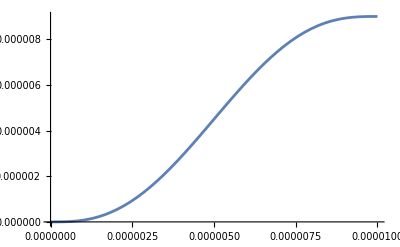

```mathematica
Plot[1/1000000 9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5),{t,0,T}]
```

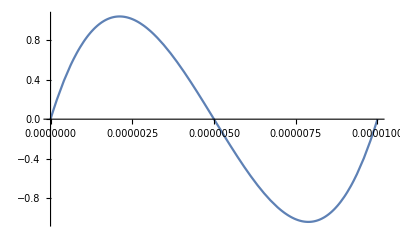

```mathematica
Plot[54/5 (100000 t-30000000000 t^2+2000000000000000 t^3)+(9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5))/1000000,{t,0,T}]
```

```mathematica
Simplify[54/5 ⋅ (100000 t-30000000000 ⋅ t^2+2000000000000000 ⋅ t^3)+1/1000000 9 ⋅[10000000000000000 ⋅ t^3-1500000000000000000000 ⋅ t^4+60000000000000000000000000 ⋅ t^5]]
```

1080000 ⋅ t (1+100000 ⋅ t (-3+200000 t))+(9 ⋅[10000000000000000 ⋅ t^3 (1-150000 t+6000000000 t^2)])/1000000

1080000*⋅*t*(1 + 100000*⋅*t*(-3 + 200000*t)) + (9*⋅[10000000000000000*⋅*t^3*(1 - 150000*t + 6000000000*t^2)])/1000000

WolframAlphaQueryResults

```mathematica
Plot[1080000 ⋅ t (1+100000 ⋅ t (-3+200000 t))+(9 ⋅[10000000000000000 ⋅ t^3 (1-150000 t+6000000000 t^2)])/1000000,{t,0,10^-5}]
```

-Graphics-

```mathematica
t=1;1080000 ⋅ t (1+100000 ⋅ t (-3+200000 t))+(9 ⋅[10000000000000000 ⋅ t^3 (1-150000 t+6000000000 t^2)])/1000000
```

1080000 ⋅ (1+19999700000 ⋅)+(9 ⋅[59998500010000000000000000 ⋅])/1000000

```mathematica
1/1000000 9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5)
```

(9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5))/1000000

```mathematica
Simplify[(9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5))/1000000]
```

90000000000 t^3 (1-150000 t+6000000000 t^2)

```mathematica
90000000000
```

90000000000

```mathematica
ScientificForm[N[90000000000,11]]
```

9.0000000000×10^10

```mathematica
-150000*90000000000
```

-13500000000000000

```mathematica
ScientificForm[N[-13500000000000000,17]]
```

-1.3500000000000000×10^16

```mathematica
6000000000*90000000000
```

540000000000000000000

```mathematica
ScientificForm[N[540000000000000000000,21]]
```

5.40000000000000000000×10^20

```mathematica
(30 ⋅ L ((2 ⋅ t^3)/T^3-(3 ⋅ t^2)/T^2+t/T))/(T^2 ω)+L ⋅[(6 ⋅ t^5)/T^5-(15 ⋅ t^4)/T^4+(10 ⋅ t^3)/T^3]
```

(30 ⋅ L ((2 ⋅ t^3)/T^3-(3 ⋅ t^2)/T^2+t/T))/(T^2 ω)+L ⋅[(6 ⋅ t^5)/T^5-(15 ⋅ t^4)/T^4+(10 ⋅ t^3)/T^3]

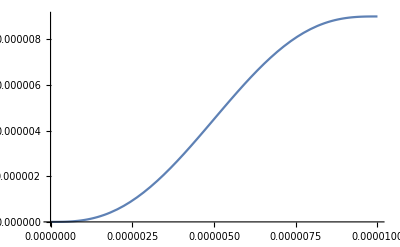

```mathematica
Clear[t];ω=250000;T=10^-5;L=9*10^-6;Plot[L *((6 *t^5)/T^5-(15 *t^4)/T^4+(10 *t^3)/T^3),{t,0,T}]
```

```mathematica
L *((6 *t^5)/T^5-(15 *t^4)/T^4+(10 *t^3)/T^3)
```

1/1000000 9 (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5)

```mathematica
{-32.51139646,-23.78228871,-16.42517293,-9.66883447,-3.19470848,3.19470848,9.66883447,16.42517293,23.78228871,32.51139646}
```

{-32.5114,-23.7823,-16.4252,-9.66883,-3.19471,3.19471,9.66883,16.4252,23.7823,32.5114}

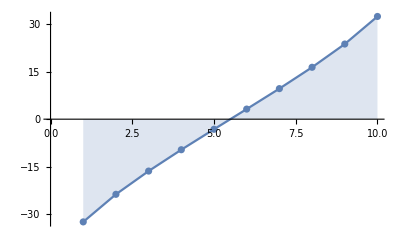

```mathematica
ListPlot[{-32.51139646,-23.78228871,-16.42517293,-9.66883447,-3.19470848,3.19470848,9.66883447,16.42517293,23.78228871,32.51139646},Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Differences[{-32.51139646,-23.78228871,-16.42517293,-9.66883447,-3.19470848,3.19470848,9.66883447,16.42517293,23.78228871,32.51139646}]
```

{8.72911,7.35712,6.75634,6.47413,6.38942,6.47413,6.75634,7.35712,8.72911}

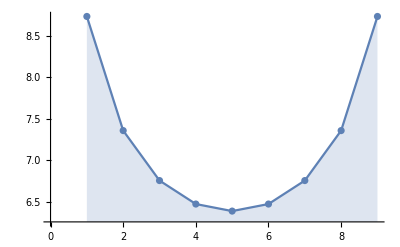

```mathematica
ListPlot[{8.72910775,7.357115780000001,6.7563384599999985,6.47412599,6.38941696,6.47412599,6.7563384599999985,7.357115780000001,8.72910775},Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Clear[t,L];ω=250000;T=10^-5;L *10^-6*((6 *t^5)/T^5-(15 *t^4)/T^4+(10 *t^3)/T^3)
```

1/1000000 L (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5)

```mathematica
Simplify[1/1000000 L (10000000000000000 t^3-1500000000000000000000 t^4+60000000000000000000000000 t^5)]
```

10000000000 L t^3 (1-150000 t+6000000000 t^2)

```mathematica
ScientificForm[N[6000000000,10]]
```

6.000000000×10^9

```mathematica
ScientificForm[N[10000000000,11]]
```

1.0000000000×10^10

```mathematica
8.729+7.357+6.756+6.474+6.389+6.474+6.756+7.357+8.729
```

65.021

```mathematica
8.729+7.357+6.756+6.474+6.389+6.474+6.756+7.357
```

56.292

```mathematica
(*For 9 ions*)
```

```mathematica
{-30.35324121,-21.40035665,-13.81017777,-6.79008617,-0.,6.79008617,13.81017777,21.40035665,30.35324121}
```

{-30.3532,-21.4004,-13.8102,-6.79009,0.,6.79009,13.8102,21.4004,30.3532}

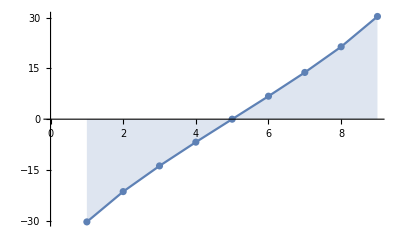

```mathematica
ListPlot[{-30.35324121,-21.40035665,-13.81017777,-6.79008617,-0.,6.79008617,13.81017777,21.40035665,30.35324121},Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
Differences[{-30.35324121,-21.40035665,-13.81017777,-6.79008617,-0.,6.79008617,13.81017777,21.40035665,30.35324121}]
```

{8.95288,7.59018,7.02009,6.79009,6.79009,7.02009,7.59018,8.95288}

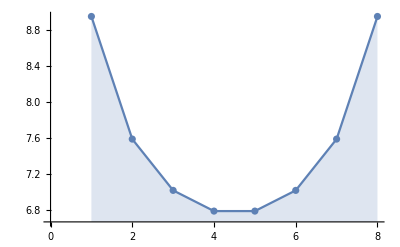

```mathematica
ListPlot[{8.952884560000001,7.59017888,7.020091599999999,6.79008617,6.79008617,7.020091599999999,7.59017888,8.952884560000001},Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
8.952+7.590+7.020+6.790+6.790+7.020+7.590+8.953
```

60.705

```mathematica
8.952+7.590+7.020+6.790+6.790+7.020+7.590
```

51.752

```mathematica
8.952+7.590+7.020+6.790+6.790+7.020
```

44.162

```mathematica
8.952+7.590+7.020+6.790+6.790
```

37.142

```mathematica
8.952+7.590+7.020+6.790
```

30.352

```mathematica
8.952+7.590+7.020
```

23.562

```mathematica
8.952+7.590
```

16.542

```mathematica
8.952
```

8.952

```mathematica
Clear[t];ω=250000;T=3.5*10^-5;L=74.967*10^-6;L *((6 *t^5)/T^5-(15 *t^4)/T^4+(10 *t^3)/T^3)
```

0.000074967 (2.33236×10^14 t^3-9.99584×10^18 t^4+1.14238×10^23 t^5)

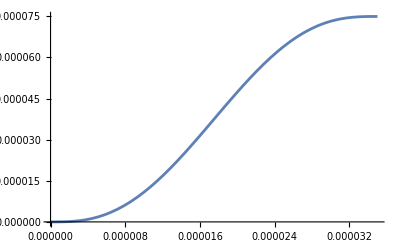

```mathematica
Plot[0.00007496699999999999 (2.3323615160349847*^14 t^3-9.995835068721363*^18 t^4+1.1423811507110128*^23 t^5),{t,0,T}]
```

```mathematica
0.00007496699999999999 (2.3323615160349847*^14 t^3-9.995835068721363*^18 t^4+1.1423811507110128*^23 t^5)
```

0.000074967 (2.33236×10^14 t^3-9.99584×10^18 t^4+1.14238×10^23 t^5)

```mathematica
Simplify[0.00007496699999999999 (2.3323615160349847*^14 t^3-9.995835068721363*^18 t^4+1.1423811507110128*^23 t^5)]
```

t^3 (1.7485×10^10-7.49358×10^14 t+8.56409×10^18 t^2)

```mathematica
Simplify[0.000056291999999999996 (2.3323615160349847*^14 t^3-9.995835068721363*^18 t^4+1.1423811507110128*^23 t^5)]
```

t^3 (1.31293×10^10-5.62686×10^14 t+6.43069×10^18 t^2)

```mathematica
3200/(10000*18*60)
```

1/3375

```mathematica
N[1/3375]
```

0.000296296

```mathematica
(304+280)/23
```

584/23

```mathematica
N[584/23]
```

```mathematica
25.391304347826086/2
```

12.6957